Solution to general 4 state model with forward k rates and reverse r rates

```mathematica
ass={ koff>0 , km>0, kp>0, kon>0, koff0<koff1, koff0>0, koff1>0, b > 1};
```

```mathematica
sys={k1 p1 - r1 p2, k2 p2 - r2 p3, k3 p3 - r3 p4, k4 p4 - r4 p1, p1+p2+p3+p4}
```

{k1 p1-p2 r1,k2 p2-p3 r2,k3 p3-p4 r3,k4 p4-p1 r4,p1+p2+p3+p4}

```mathematica
sys = sys/.{k1-> kon, r1-> koff, k3-> koff, r3-> kon, k2->  kp, r2-> km, k4-> b km, r4->  kp};
sys = sys /. {km-> 1} (* nondim to km *)
```

{kon p1-koff p2,kp p2-p3,koff p3-kon p4,-kp p1+b p4,p1+p2+p3+p4}

```mathematica
sol = FullSimplify[Solve[{J,J,J,J,1}==sys, {J, p1,p2,p3,p4}]]
```

{{J→((-1+b) koff kon kp)/((koff+kon) (kon+kp+b (1+koff+kp)+kp (koff+kon+kp))),p1→(koff (kon+b (1+koff+kp)))/((koff+kon) (kon+kp+b (1+koff+kp)+kp (koff+kon+kp))),p2→(kon (b+b koff+kon+kp))/((koff+kon) (kon+kp+b (1+koff+kp)+kp (koff+kon+kp))),p3→(kon kp (b+koff+kon+kp))/((koff+kon) (kon+kp+b (1+koff+kp)+kp (koff+kon+kp))),p4→(koff kp (1+koff+kon+kp))/((koff+kon) (kon+kp+b (1+koff+kp)+kp (koff+kon+kp)))}}

We are treating state 3 as the productive state - i.e. the one in which transcription happens.

```mathematica
p3cb[koff_] = p3/. sol[[1]]
```

(kon kp (b+koff+kon+kp))/((koff+kon) (kon+kp+b (1+koff+kp)+kp (koff+kon+kp)))

```mathematica
p3c[koff_] = FullSimplify[p3cb[koff] /. {b -> 1}]
```

(kon kp)/(koff+kon+koff kp+kon kp)

```mathematica
p3cb[c*koff]
```

(kon kp (b+c koff+kon+kp))/((c koff+kon) (kon+kp+b (1+c koff+kp)+kp (c koff+kon+kp)))

#### Calculate fidelity ratios in/out of equilibrium

```mathematica
eqRatio = FullSimplify[p3c[koff] / p3c[c*koff]]
noneqRatio = FullSimplify[p3cb[koff] / p3cb[c*koff]]
```

(c koff+kon)/(koff+kon)

((c koff+kon) (b+koff+kon+kp) (kon+kp+b (1+c koff+kp)+kp (c koff+kon+kp)))/((koff+kon) (b+c koff+kon+kp) (kon+kp+b (1+koff+kp)+kp (koff+kon+kp)))

### Optimum Achieved when Beta >> ckoff >> km, kp, kon

```mathematica
fidelityInfBeta = Limit[noneqRatio , b->Infinity]
```

(c koff+c^2 koff^2+kon+c koff kon+c koff kp+kon kp)/(koff+koff^2+kon+koff kon+koff kp+kon kp)

```mathematica
fidelityInfKoff = Limit[fidelityInfBeta , koff->Infinity]
```

c^2

```mathematica
concRatio= noneqRatio/. {kp-> 1, kon-> 1, c-> 10};
concRatio = FullSimplify[concRatio]
```

(2 (2+b+koff) (1+10 koff) (2+b+5 (1+b) koff))/((1+koff) (2+b+10 koff) (4+koff+b (2+koff)))

```mathematica
Limit[concRatio,b->Infinity]
```

(2+30 koff+100 koff^2)/(2+3 koff+koff^2)

```mathematica
concFunction[koff_,b_] = concRatio /100;
```

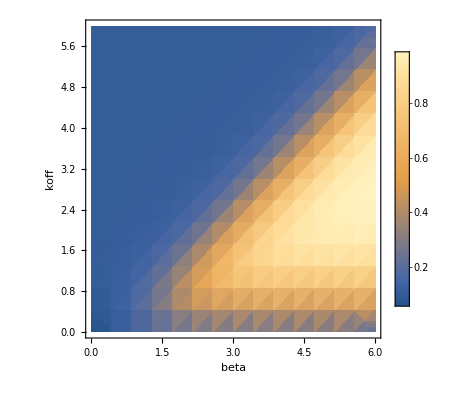

```mathematica
DensityPlot[concFunction[koff,b],{b,1,10^6},{koff,1,10^6},FrameLabel->{"beta","koff"},PlotRange->All,,PlotLegends->Automatic, ScalingFunctions->{"Log10","Log10"}]
```

```mathematica
errorRate[koff_,b_] = .5*( p3cb[koff]*(1/concRatio - 1) + 1) /. {kon->1,kp->1}
```

0.5 (1+((2+b+koff) (-1+((1+koff) (2+b+10 koff) (4+koff+b (2+koff)))/(2 (2+b+koff) (1+10 koff) (2+b+5 (1+b) koff))))/((1+koff) (4+koff+b (2+koff))))

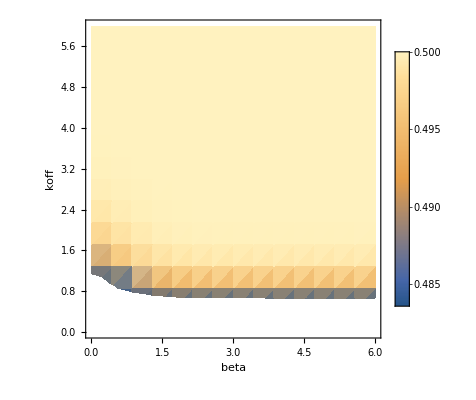

```mathematica
DensityPlot[errorRate[koff,b],{b,1,10^6},{koff,1,10^6},FrameLabel->{"beta","koff"},PlotLegends->Automatic, ScalingFunctions->{"Log10","Log10"}]
```

```mathematica
N[p3cb[1] /. {b->10,kp-> 1,kon->1}]
```

0.185714